## Execute all

```mathematica
SetDirectory[NotebookDirectory[]<>"/data"];
```

```mathematica
directories=Select[ToExpression[SortBy[Select[FileNames[],DirectoryQ],ToExpression[#]&]],IntegerQ]
```

{256,512,768,1024,1536,2048}

This equals the box sizes of the simulations, up to normalization of polymer length L=6.3. Below L_box is given in units of L.

```mathematica
boxtimes=Table[Import[ToString@x<>"/boxfixationtimes.mx"],{x,directories}];
localtimes=Table[Import[ToString@x<>"/localfixationtimes.mx"],{x,directories}];
polartimes=Table[Import[ToString@x<>"/polarfixationtimes.mx"],{x,directories}];
nematictimes=Table[Import[ToString@x<>"/nematicfixationtimes.mx"],{x,directories}];
totaltimes=Table[Import[ToString@x<>"/totalfixationtimes.mx"],{x,directories}];
```

```mathematica
totallocaltimes=Table[Table[{directories[[i]],localtimes[[i,s]]},{s,1,Length@localtimes[[i]]}],{i,1,Length@directories}];
totalboxtimes=Table[Table[{directories[[i]],boxtimes[[i,s]]},{s,1,Length@boxtimes[[i]]}],{i,1,Length@directories}];
totalpolartimes=Table[Table[{directories[[i]],polartimes[[i,s]]},{s,1,Length@polartimes[[i]]}],{i,1,Length@directories}];
totalnematictimes=Table[Table[{directories[[i]],nematictimes[[i,s]]},{s,1,Length@nematictimes[[i]]}],{i,1,Length@directories}];
totaltotaltimes=Table[{directories[[i]],totaltimes[[i]]},{i,1,Length@directories}];
```

```mathematica
totalmeanlocaltime=Mean/@totallocaltimes
totalmeanboxtime=Mean/@totalboxtimes
totalmeanpolartime=Mean/@totalpolartimes
totalmeannematictime=DeleteCases[Mean/@totalnematictimes,Mean[{}]]
```

{{256,182.431},{512,256.411},{768,281.207},{1024,280.777},{1536,273.766},{2048,235.33}}

{{256,3187.15},{512,3879.99},{768,4373.26},{1024,4277.34},{1536,7207.05},{2048,10835.4}}

{{256,6137.2},{512,7461.},{768,8077.5},{1024,15683.3},{1536,23295.},{2048,34704.1}}

{{512,8912.11},{768,9066.64},{1024,13296.},{1536,18766.8},{2048,18076.6}}

### Plot with all events

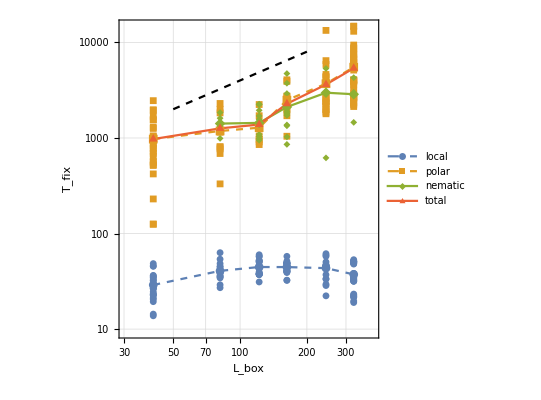

```mathematica
timenorm=6.3;
plt=Show[{ListLogLogPlot[{Flatten[totallocaltimes,1],Flatten[totalpolartimes,1],Flatten[totalnematictimes,1]}/timenorm,PlotRange->{{30,400},All},GridLines->Automatic,PlotMarkers->{Automatic,7}],ListLogLogPlot[{totalmeanlocaltime,totalmeanpolartime,totalmeannematictime,totaltotaltimes}/timenorm,PlotStyle->{Dashed,Dashed,Thick,Thick,Thick},PlotMarkers->Automatic,Joined->True,PlotLegends->{"local","polar","nematic","total"}],LogLogPlot[40x,{x,50,200},PlotStyle->{Black,Dashed},PlotLegends->"--L_box"]},Frame->True,AspectRatio->1,FrameLabel->{Style["L_box",14],Style["T_fix",14]}]
```

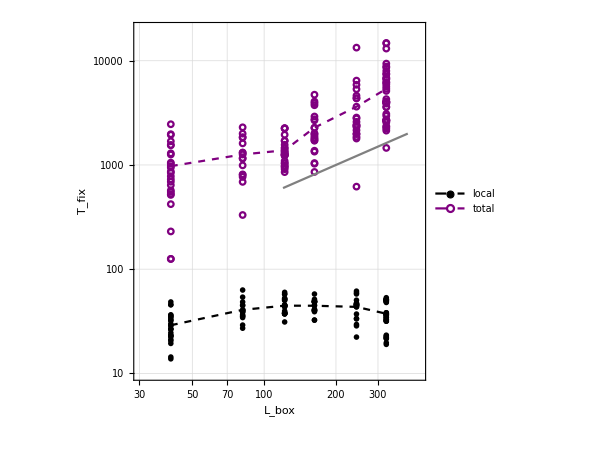

```mathematica
plotcolor1=Purple;
plotcolor2=Black;
plotmarker1=Circle[];
plotmarker2=Disk[];
plot1=Show[{ListLogLogPlot[{Flatten[totallocaltimes,1],Flatten[totalpolartimes,1],Flatten[totalnematictimes,1]}/timenorm,PlotRange->{{30,450},{10,20000}},GridLines->Automatic,PlotMarkers->{{Graphics[{plotcolor2,Thin,plotmarker2}],0.01},{Graphics[{plotcolor1,Thin,plotmarker1}],0.02},{Graphics[{plotcolor1,Thin,plotmarker1}],0.02}}],ListLogLogPlot[{totalmeanlocaltime,totaltotaltimes}/timenorm,PlotStyle->{{Dashed,plotcolor2},{Dashed,plotcolor1}},PlotMarkers->{{Graphics[{plotcolor2,Thin,plotmarker2}],0.01},{Graphics[{plotcolor1,Thin,plotmarker1}],0.02}},Joined->True,PlotLegends->{"local","total"}],LogLogPlot[5x,{x,120,400},PlotStyle->{Gray,Thick},PlotLegends->"--L_box"]},Frame->True,AspectRatio->1,FrameLabel->{Style["L_box",18,Black],Style["T_fix",18,Black]},FrameTicksStyle->Directive[Black,18],ImageSize->450]
```

### Plot with all events, including quantiles

```mathematica
Manipulate[test=Quantile[#,{d,1-d}]&/@MapThread[Flatten[{#1,#2}]&,{polartimes,nematictimes}];
Show[{plot1,ListLogLogPlot[{Thread[{directories,test[[;;,1]]}],Thread[{directories,test[[;;,2]]}]}/6.3,Joined->True]}]
,{d,0.01,0.4}]
```

### Plot with all events, including 15th and 85th percentiles

```mathematica
Options[errListPlot]={Filling->{1->{2}},Joined->{False,False,True},PlotStyle->{Black,Black,Directive[Opacity[0.6],Blue]},FillingStyle->Black,PlotMarkers->{Graphics@Line[.04 {{-1,0},{1,0}}],Graphics@Line[.04 {{-1,0},{1,0}}],""}};
errListPlot[plotFun_,data_,opts:OptionsPattern[]]:=Block[{},plotFun[{{#[[1]],#[[3,1]]}&/@data,{#[[1]],#[[3,2]]}&/@data,data[[;;,{1,2}]]},opts,Sequence@@Options[errListPlot]]]
```

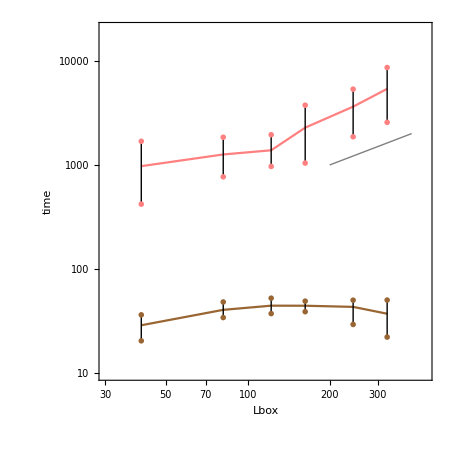

```mathematica
percentiles1=Quantile[#,{0.15,0.85}]&/@MapThread[Flatten[{#1,#2}]&,{polartimes,nematictimes}];
data1=Table[{directories[[i]],totaltimes[[i]],percentiles1[[i]]}/6.3,{i,1,Length@directories}];
percentiles2=Quantile[#,{0.15,0.85}]&/@localtimes;
data2=Table[{directories[[i]],totalmeanlocaltime[[i,2]],percentiles2[[i]]}/6.3,{i,1,Length@directories}];
p1=errListPlot[ListLogLogPlot,data1,PlotStyle->{Pink},PlotRange->{{30,450},{10,20000}},Frame->True,GridLines->Automatic,FrameLabel->{"Lbox","time"},ImageSize->450,AspectRatio->1,BaseStyle->{18,FontFamily->"Arial"}];
p2=errListPlot[ListLogLogPlot,data2,PlotStyle->{Brown},PlotRange->{{30,450},{10,20000}},Frame->True,GridLines->Automatic,FrameLabel->{"Lbox","time"},ImageSize->450,AspectRatio->1,BaseStyle->{18,FontFamily->"Arial"}];
pp2=Show[{p1,p2,LogLogPlot[5x,{x,200,400},PlotStyle->{Gray,Thick}]}]
```